```mathematica
cx[t_]:=1.5*t*Exp[-0.6t]+0.1*Sin[28.2t]Exp[-0.8t];
cy[t_]:=(1-Exp[-0.1t^2]-0.25*Sin[7.5t]Exp[-0.8t]);


V[x_,a_,b_,c_]:=a+b*(c+x^2)^2
Manipulate[
Show[
RevolutionPlot3D[
V[x,a,b,c],{x,0,1},{q,0,2 Pi},
PlotPoints->30,
PlotStyle->Opacity[0.9],
Mesh->10,
MeshStyle->Opacity[0.5],
SphericalRegion->True,
BoxRatios->{1,1,1},
ImageSize->400,
Boxed->False,
AxesStyle -> Arrowheads[{0.0, 0.05}],
PlotRange->{{-1.5,1},{-1.5,1},{-1.5,1}},
ViewPoint->{-2,-2,3},
Axes->False
],
Graphics3D[{Red,Sphere[{sx,sy,V[Sqrt[sx*sx+sy*sy]+0.15,a,b,c]},0.15]}],
Graphics3D[{Arrow[{{-1,-1,-1}, {0,-1, -1}}],Text[Style["σ", 14], {0,-1.1,-1}]}],
Graphics3D[{Arrow[{{-1,-1,-1}, {-1,0, -1}}],Text[Style["π", 14], {-1.1,0, -1}]}]
,ParametricPlot3D[
{√(Abs@0.5)(1-t),0,0.05+V[Sqrt[Abs@(0.5)*(1-t)(1-t)],a,b,c]},{t,0,1},
PlotStyle -> Directive[{Red, Arrowheads[.06]}]]/. 
  Line[pts_] :> Arrow[Tube[pts, .02], {0, 0}]
(*,ParametricPlot3D[
{√(Abs@c)cy[t],-√(Abs@c)*cx[t],V[Sqrt[Abs@(c)*cx[t]*cx[t]+Abs@(c)*cy[t]*cy[t]],a,b,c]},{t,0,12},
PlotStyle -> Directive[{Red, Arrowheads[.06]}]]/. 
  Line[pts_] :> Arrow[Tube[pts, .02], {0, 0}]*)
],
{{a,-1},-2,1},{{b,0.8},0,5},{{c,0.1},-1,1},{{sx,Sqrt@0.5},-1,1},{{sy,0},-1,1}]
```

√s=0.479-0.558 ⅈ

input mass (test): 0.596259

input Γ (test): 0.63863

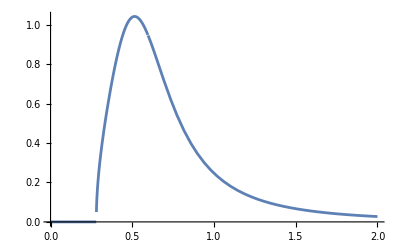

```mathematica
mπ:=0.14;

Mp:=0.479
Γp:=2*0.279

Γ:=0.64;
Γ:=Sqrt@(1/2 (16 mπ^2+Γp^2-4 Mp^2+√(16 Γp^2 Mp^2+(-16  mπ^2-Γp^2+4 Mp^2)^2)))
mσ:=0.55;
mσ:=Sqrt@(1/4 (16 mπ^2+√(16 Γp^2 Mp^2+(-16 mπ^2-Γp^2 +4 Mp^2)^2)))
Δ[s_]:=1/(s-mσ^2+ⅈ*Γ*√(s-(2*mπ)^2))
S[k_]:=-1/π*Im[Δ[k^2]]
Solve[0==1/Δ[s],s];
(2mσ^2-Γ^2)/2-√(Γ^4/4+Γ^2*((2*mπ)^2-mσ^2));
sqrts=Sqrt[s]/.Solve[0==1/Δ[s],s][[1]][[1]];
Mpt=Re@sqrts;
Γpt=-2*Im@sqrts;
Print["√s=",Mpt-ⅈ*Γpt]
mσ^2-Γ^2/2==Mpt^2-Γpt^2/4;
Γ^4/4+Γ^2((2mπ)^2-mσ^2)==-Mpt^2Γpt^2;
Print["input mass (test): ",Sqrt@(1/4 (16 mπ^2+√(16 Γpt^2 Mpt^2+(-16 mπ^2-Γpt^2 +4 Mpt^2)^2)))]
Print["input Γ (test): ",Sqrt@(1/2 (16 mπ^2+Γpt^2-4 Mpt^2+√(16 Γpt^2 Mpt^2+(-16  mπ^2-Γpt^2+4 Mpt^2)^2)))]
Plot[S[k],{k,0,2}]
```

```mathematica
Γ
```

0.63863

```mathematica
m
```

```mathematica
NIntegrate[2*k*S[k],{k,0.28,1.5}]
```

0.718627

```mathematica
mpi=140;
msig=500;
g=12.8;
c[k_]=1-(4*mpi^2)/k^2;
I0[k_]=1/(2 √c[k])Log[Abs[(√c[k]-1)/(√c[k]+1)]];
ReS[k2_]=-(3g^2k2)/(64π^2)(2/3-c[k]+(c[k]-c[k]^2)I0[k]);
ImS[k2_]=-(3g^2)/(32π^2)mpi^2 √(1-(4*mpi^2)/k2);
f[k_]=(-2π*ImS[k^2])/((k^2-msig^2-ReS[k^2])^2+ImS[k^2]^2);
```

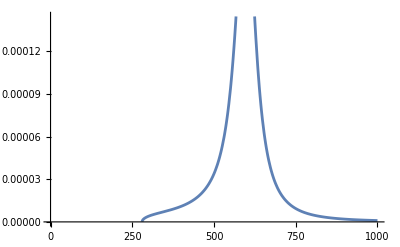

```mathematica
Plot[f[x],{x,0,1000}]
```

```mathematica
NIntegrate[k*f[k],{k,2*mpi,Infinity}]
```

14.9156

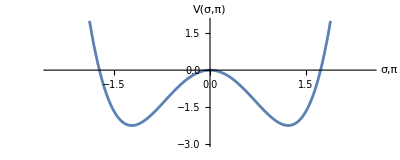

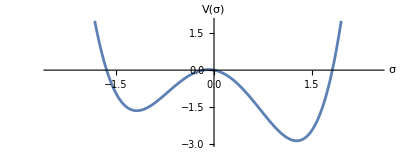

/home/tobiasb/OneDrive/projects/SoftPionsPresentation/images/MexHat1D.png

/home/tobiasb/OneDrive/projects/SoftPionsPresentation/images/MexHat1D_SymBr.png

```mathematica
p1=Plot[{x^4-3x^2},{x,-2,2},PlotRange->{{-2.5,2.5},{-3,2}},AxesStyle->Arrowheads[{0.0,0.05}],Ticks->None,AxesLabel->{Style["σ,π",16],Style["V(σ,π)",16]},
ImageSize->400,
AspectRatio->1/2.5
]
p2=Plot[{x^4-3x^2-0.5x},{x,-2,2},PlotRange->{{-2.5,2.5},{-3,2}},AxesStyle->Arrowheads[{0.0,0.05}],Ticks->None,AxesLabel->{Style["σ",16],Style["V(σ)",16]},
ImageSize->400,
AspectRatio->1/2.5
]
Export["/home/tobiasb/OneDrive/projects/SoftPionsPresentation/images/MexHat1D.png",p1]
Export["/home/tobiasb/OneDrive/projects/SoftPionsPresentation/images/MexHat1D_SymBr.png",p2]
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

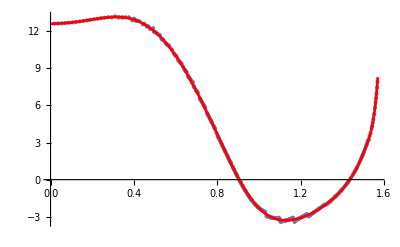

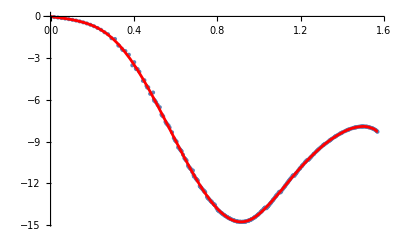

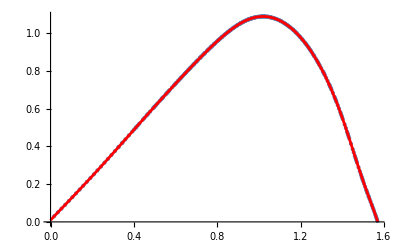

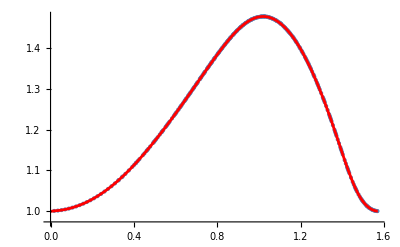

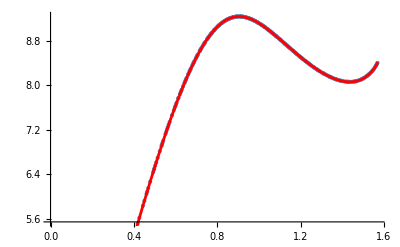

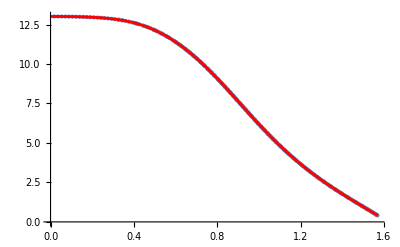

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)

ndegree=55;(*14,25,43,44,55*)
monomials=Table[x^i,{i,0,ndegree}];
ur[α_]=Fit[Transpose@{αs,urs},monomials,x]/.x->α;
uτ[α_]=Fit[Transpose@{αs,uτs},monomials,x]/.x->α;
r[α_]=Fit[Transpose@{αs,rs},monomials,x]/.x->α;
Dr[α_]=Fit[Transpose@{αs,Drs},monomials,x]/.x->α;
τ[α_]=Fit[Transpose@{αs,τs},monomials,x]/.x->α;
Dτ[α_]=Fit[Transpose@{αs,Dτs},monomials,x]/.x->α;
Show[
ListPlot[Transpose@{αs,Drs}],
Plot[Dr[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,Dτs}],
Plot[Dτ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,urs}],
Plot[ur[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,uτs}],
Plot[uτ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,rs}],
Plot[r[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,τs}],
Plot[τ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
```

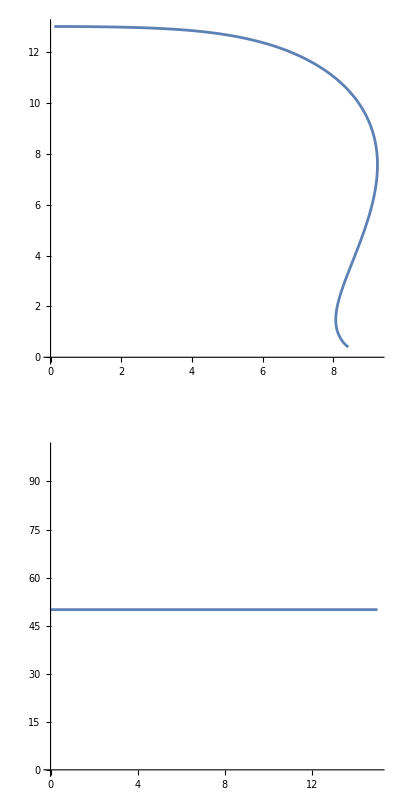

```mathematica
p1=ParametricPlot[
{r[α],τ[α]},{α,0,π/2},
ImageSize->200,
AspectRatio->1];
p2=ParametricPlot[
{15*x,50},{x,0,1},
ImageSize->200,
AspectRatio->1];
GraphicsColumn[{p1,p2}]
```